# ParetoPrinciplePlot

Makes Pareto principle adherence plots

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
Clear[ParetoDataSpecQ];
ParetoDataSpecQ[data_]:=MatchQ[data,{((Tooltip|Callout)[(Tooltip|Callout)[{_?NumericQ...},__],__]|(Tooltip|Callout)[{_?NumericQ...},__]|{_?NumericQ...})..}]||MatchQ[data,{{_?NumericQ...}..}];
```

```mathematica
Clear[ParetoGetData];
ParetoGetData[data:{(Tooltip|Callout)[{_?NumericQ...},__]..}]:=data⟦All,1⟧;
ParetoGetData[data:{((Tooltip|Callout)[(Tooltip|Callout)[{_?NumericQ...},__],__]|(Tooltip|Callout)[{_?NumericQ..},__]|{_?NumericQ...})..}]:=Cases[data,{_?NumericQ...},3];
ParetoGetData[data:{{_?NumericQ...}..}]:=data;
```

```mathematica
Clear[ParetoPrinciplePlot];
```

```mathematica
ParetoPrinciplePlot::args="The first argument is expected to be a numerical vector or a list of numerical vectors.";
```

```mathematica
ParetoPrinciplePlot::pgl="The value of the option \"ParetoGridLines\" is expected to be Automatic or a list of two numerical vectors, each with numbers between 0 and 1.";
```

```mathematica
Options[ParetoPrinciplePlot]=Join[{"Tooltip"->True,"ParetoGridLines"->Automatic},Options[ListPlot]];
```

```mathematica
ParetoPrinciplePlot[dataVec:{_?NumericQ...},opts:OptionsPattern[]]:=
ParetoPrinciplePlot[{dataVec},opts];
```

```mathematica
ParetoPrinciplePlot[dataVecs:{{_?NumericQ...}..},opts:OptionsPattern[]]:=
Block[{tooltipQ,t},

tooltipQ=TrueQ[OptionValue[ParetoPrinciplePlot,"Tooltip"]];
t=Map[Accumulate[#]/Total[#]&,ReverseSort/@dataVecs];

If[tooltipQ,
t=MapThread[Tooltip,{t,Range[Length[dataVecs]]}]
];

ParetoPrinciplePlotFrame[t,FilterRules[{opts},Options[ParetoPrinciplePlotFrame]]]
];
```

```mathematica
ParetoPrinciplePlot[dataVecs:{(Tooltip|Callout)[{_?NumericQ...},__]..},opts:OptionsPattern[]]:=
Block[{t},
t=Map[#⟦0⟧[(Accumulate[#]/Total[#]&)[ReverseSort[#⟦1⟧]],Sequence@@Rest[#]]&,dataVecs];
ParetoPrinciplePlotFrame[t,FilterRules[{opts},Options[ParetoPrinciplePlotFrame]]]
];
```

```mathematica
ParetoPrinciplePlot[dataVecs:{((Tooltip|Callout)[(Tooltip|Callout)[{_?NumericQ...},__],__]|(Tooltip|Callout)[{_?NumericQ...},__]|{_?NumericQ...})..},opts:OptionsPattern[]]:=
Block[{t},
t=dataVecs/.x:{_?NumberQ..}:>(Accumulate[#]/Total[#]&)[ReverseSort[x]];
ParetoPrinciplePlotFrame[t,FilterRules[{opts},Options[ParetoPrinciplePlotFrame]]]
];
```

```mathematica
ParetoPrinciplePlot[___]:=
Block[{},
Message[ParetoPrinciplePlot::args];
$Failed
];
```

```mathematica
Clear[ParetoPrinciplePlotFrame];
Options[ParetoPrinciplePlotFrame]=Join[{"MaxParetoFraction"->0.5,"ParetoGridLines"->Automatic},Options[ListPlot]];
ParetoPrinciplePlotFrame[t_?ParetoDataSpecQ,opts:OptionsPattern[]]:=
Block[{data=ParetoGetData[t],maxLen,paretoGridSpec,gridSpec},

paretoGridSpec=OptionValue[ParetoPrinciplePlotFrame,"ParetoGridLines"];

If[TrueQ[paretoGridSpec===Automatic],paretoGridSpec={Range[0,0.5,0.1],{0.8}}];
If[MatchQ[paretoGridSpec,{Automatic,_}],paretoGridSpec={Range[0,1,0.1],paretoGridSpec⟦2⟧}];
If[MatchQ[paretoGridSpec,{_,Automatic}],paretoGridSpec={paretoGridSpec⟦1⟧,Range[0,1,0.1]}];

If[TrueQ[paretoGridSpec===None],paretoGridSpec={{},{}}];
If[MatchQ[paretoGridSpec,{None,_}],paretoGridSpec={{},paretoGridSpec⟦2⟧}];
If[MatchQ[paretoGridSpec,{_,None}],paretoGridSpec={paretoGridSpec⟦1⟧,{}}];

Which[
!MatchQ[paretoGridSpec,{{_?NumericQ...},{_?NumericQ...}}],
Message[ParetoPrinciplePlot::pgl];
paretoGridSpec={Range[0.1,0.5,0.1],{0.8}},

!(VectorQ[paretoGridSpec⟦1⟧,0≤#≤1&]&&VectorQ[paretoGridSpec⟦2⟧,0≤#≤1&]),
Message[ParetoPrinciplePlot::pgl];
paretoGridSpec=Map[Sort[Select[#,0≤#≤1&]]&,paretoGridSpec],

True,
paretoGridSpec=Map[Sort[Select[#,0≤#≤1&]]&,paretoGridSpec];
];

maxLen=Max[Length/@data];
gridSpec={maxLen*paretoGridSpec⟦1⟧,paretoGridSpec⟦2⟧};

ListPlot[t,
FilterRules[{opts},Options[ListPlot]],
PlotRange->All,
GridLines->gridSpec,
Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Table[{maxLen*c,ToString[Round[100 c]]<>"%"},{c,paretoGridSpec⟦1⟧}]}}]
];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

ParetoPrinciplePlot[vect]

plots the normalized cumulative sum of the reverse-sorted vect.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

The adherence of the data vect to the Pareto principle can be easily verified with the plots of ParetoPrinciplePlot.

The argument can be a numerical list, a list of numerical lists, or a list of numerical lists wrapped with tooltips and callouts.

For a given numerical vector vect the Pareto principle plot data is computed with the formula: Accumulate[ReverseSort[vect]]/Total[vect].

ParetoPrinciplePlot takes all options of ListPlot.

The option "ParetoGridLines" can be used to define Pareto principle specific grid lines.

The option "Tooltip" can be used to specify the use of automatic Tooltip wrappers.

Here is the options table:

"ParetoGridLines" | Automatic | Pareto-specific grid lines.
"Tooltip" | True | whether automatic Tooltip wrappers should be used

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Pareto principle plot for a numerical vector:

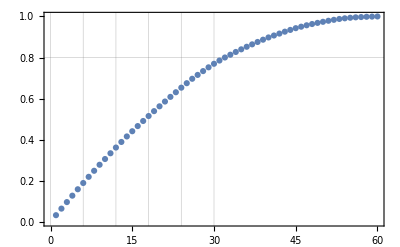

```mathematica
SeedRandom[2723]
ParetoPrinciplePlot[RandomReal[1,60]]
```

Pareto principle plot for a list of numerical vectors:

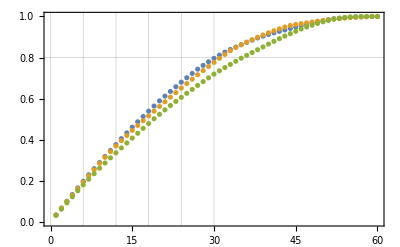

```mathematica
SeedRandom[574];
ParetoPrinciplePlot[RandomReal[1,{3,60}]]
```

### Scope

Here is a plot for a list of numerical vectors with tooltips:

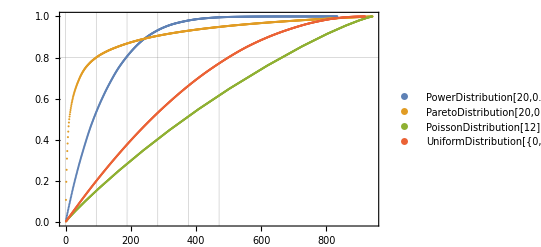

```mathematica
dists={PowerDistribution[20,0.2],ParetoDistribution[20,0.8],PoissonDistribution[12],UniformDistribution[]};ParetoPrinciplePlot[Tooltip[RandomVariate[#,RandomInteger[{800,1000}]],#]&/@dists,PlotRange->All,PlotLegends->dists]
```

Numerical vectors with nested Tooltip and Callout specifications can be given; “wrapped” and “plain” vectors can be mixed:

```mathematica
data=Map[
Switch[#,
_ParetoDistribution,
Tooltip[Callout[RandomVariate[#,RandomInteger[{800,1000}]],#,{300,Below}],#],

_UniformDistribution,
RandomVariate[#,RandomInteger[{800,1000}]],

_,
Callout[Tooltip[RandomVariate[#,RandomInteger[{800,1000}]],#],#]
]&,
dists];
```

```mathematica
dists={PowerDistribution[20,0.2],ParetoDistribution[20,0.8],PoissonDistribution[12],UniformDistribution[]};
ParetoPrinciplePlot[data,PlotLegends->dists,ImageSize->Large,PlotRange->All]
```

-Graphics-

### Options

#### "ParetoGridLines"

Here is a data vector:

```mathematica
SeedRandom[232]
data=Join[RandomReal[1,1000],RandomReal[{0,0.3},2000]];
```

Here is a table that shows Pareto principle adherence plots with different Pareto grid lines specifications:

```mathematica
Multicolumn[Map[Labeled[ParetoPrinciplePlot[data,ImageSize->300,"ParetoGridLines"->#],Style[#,Purple,Bold]]&,{Automatic,{Automatic,Automatic},{Automatic,None},{None,Automatic},{Automatic,Range[0,1,0.25]},{Range[0,1,0.25],Range[0,1,0.5]}}],3,Dividers->All]
```

-Graphics-

The option "ParetoGridLines" is overridden by ListPlot‘s option GridLines:

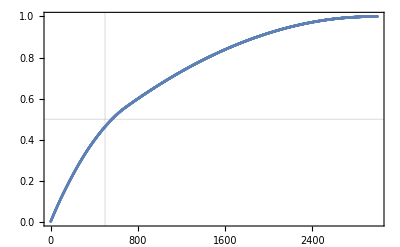

```mathematica
ParetoPrinciplePlot[data,"ParetoGridLines"->{Automatic,Automatic},GridLines->{{500},{0.5}}]
```

#### "Tooltip"

The option "Tooltip" takes Boolean values:

```mathematica
SeedRandom[2323];
data=Table[Join[RandomReal[1,1000],RandomReal[{0,h},2000]],{h,{0.3,0.4,0.6}}];
```

```mathematica
ParetoPrinciplePlot[data,ImageSize->Medium,"Tooltip"->#]&/@{False,True}
```

-Graphics-

### Applications

#### Words distribution in texts

Get the text of Shakespeare’s play “Hamlet”:

```mathematica
text=ResourceData["Hamlet"];
```

Convert the text to lower case and split it into words:

```mathematica
words=Select[StringSplit[ToLowerCase[text],{" ",",",".",";","?","!","...","-"}],StringLength[#]>0&];
Length[words]
```

32318

Plot the words tally values:

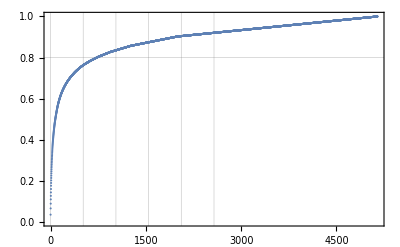

```mathematica
ParetoPrinciplePlot[Tally[words]⟦All,2⟧]
```

In the Pareto principle adherence plot above we see a clear Pareto principle manifestation: ≈15% of the words correspond to ≈80% of the text.

#### Gross Domestic Product (GDP) of countries

Pareto principle manifestation for countries GDP:

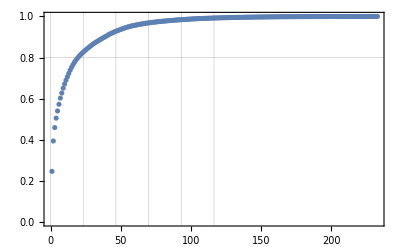

```mathematica
ParetoPrinciplePlot[QuantityMagnitude[DeleteMissing[CountryData[#,"GDP"]&/@CountryData["Countries"]]]]
```

We see that ≈10% of the countries correspond to ≈80% of the total GDP.

An interesting diagram is to plot together the curves of GDP changes for different countries in the same time period:

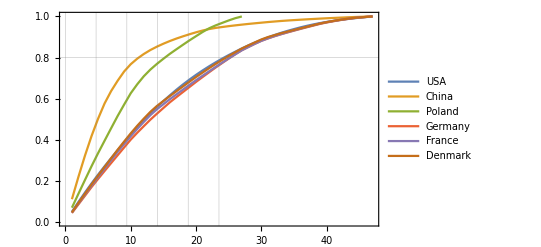

```mathematica
res=Table[(t=CountryData[countryName,{{"GDP"},{1970,2019}}];
t=Reverse@Sort[t["Path"][[All,2]]/.Quantity[x_,_]:>x];
Tooltip[t,countryName]),{countryName,{"USA","China","Poland","Germany","France","Denmark"}}];

ParetoPrinciplePlot[res,PlotRange->All,Joined->True,PlotLegends->res[[All,2]]]
```

We see that China and Poland have had rapid growth.

#### Lake data

The following code gathers lakes data and makes the Pareto principle plots for surface areas, volumes and fish catch:

```mathematica
lakeAreas=LakeData[All,"SurfaceArea"];
lakeVolumes=LakeData[All,"Volume"];
lakeFishCatch=LakeData[All,"CommercialFishCatch"];
```

```mathematica
data={lakeAreas,lakeVolumes,lakeFishCatch};
t=N@Map[QuantityMagnitude@*DeleteMissing,data];
```

We can see that the lakes area data manifests an “exaggerated” Pareto principle adherence: ≈5% of the lakes correspond to ≈90% of the total lakes area:

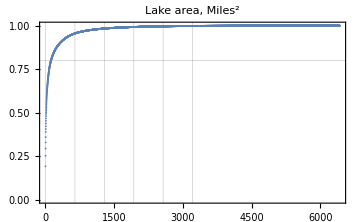
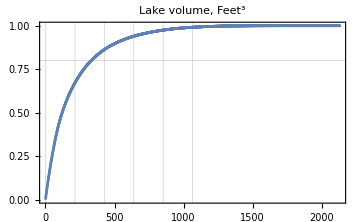
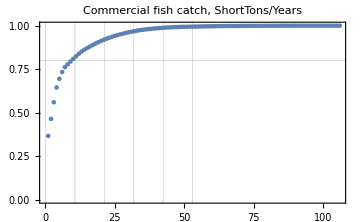

```mathematica
opts={PlotRange->All,ImageSize->Medium};MapThread[ParetoPrinciplePlot[#1,PlotLabel->Row[{#2,", ",#3}],opts]&,{t,{"Lake area","Lake volume","Commercial fish catch"},DeleteMissing[#][[1,2]]&/@data}]
```

### Properties and Relations

For a given numeric vector:

```mathematica
vec=RandomReal[1,1000];
```

The Pareto principle plot data is computed with the formula:

```mathematica
pvec=Accumulate[ReverseSort[vec]]/Total[vec];
```

Here is the corresponding plot:

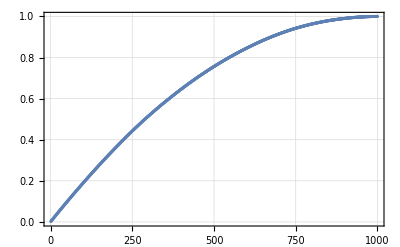

```mathematica
ListPlot[pvec,PlotTheme->"Detailed"]
```

Compare with the plot made by ParetoPrinciplePlot:

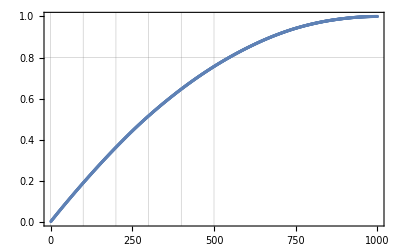

```mathematica
ParetoPrinciplePlot[vec]
```

It is beneficial to use Pareto principle adherence plots together with data summaries and histograms. Here is an example:

```mathematica
vec=QuantityMagnitude[DeleteMissing[LakeData[All,"SurfaceArea"]]];
opts={PlotTheme->"Detailed",ImageSize->300};
```

Note that the summary and histograms provide complimentary data distribution properties to those given by the Pareto principle adherence plot:

```mathematica
Grid[{
{ParetoPrinciplePlot[vec,PlotLabel->"Pareto principle adherence",opts],
Labeled[ResourceFunction["RecordsSummary"][vec],"Summary",Top]},
{Histogram[vec,Automatic,"Probability",PlotLabel->"Direct histtogram",opts],
Histogram[Log10@vec,Automatic,"Probability",PlotLabel->"Log_10 histogram",opts]}},Dividers->All]
```

-Graphics-

### Possible Issues

#### Missing values

ParetoPrinciplePlot does not work on vectors with missing values:

```mathematica
ParetoPrinciplePlot[{Missing[],10,1,20,10,12,2,7}]
```

ParetoPrinciplePlot::args: The first argument is expected to be a numerical vector or a list of numerical vectors.

$Failed

Here DeleteMissing is used in order to obtain the plot:

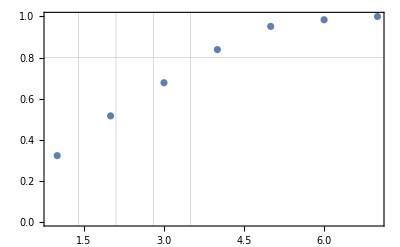

```mathematica
ParetoPrinciplePlot[DeleteMissing[{Missing[],10,1,20,10,12,2,7}]]
```

ParetoPrinciplePlot does not work on QuantityArray objects and lists of Quantity objects. Here is a list of quantity objects:

```mathematica
Shallow[DeleteMissing[lakeAreas=LakeData[All,"SurfaceArea"]]]
```

{Quantity[0.386102,Power[«2»]],Quantity[772.204,Power[«2»]],Quantity[0.0265634,Power[«2»]],Quantity[0.0525099,Power[«2»]],Quantity[0.212508,Power[«2»]],Quantity[0.155213,Power[«2»]],Quantity[0.123553,Power[«2»]],Quantity[1.8919,Power[«2»]],Quantity[0.0254827,Power[«2»]],Quantity[424.712,Power[«2»]],«6413»}

```mathematica
ParetoPrinciplePlot[DeleteMissing[lakeAreas]]
```

ParetoPrinciplePlot::args: The first argument is expected to be a numerical vector or a list of numerical vectors.

$Failed

Here both DeleteMissing and QuantityMagnitude are used in order to obtain the plot:

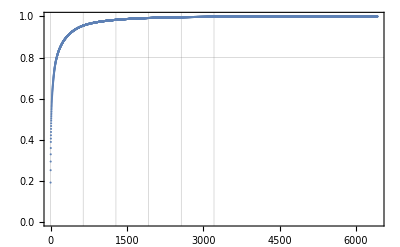

```mathematica
ParetoPrinciplePlot[QuantityMagnitude[DeleteMissing[lakeAreas]]]
```

### Neat Examples

Pareto principle adherence plots for word tallies for different translations of the United Nations’ “Universal declaration of human rights official document”:

```mathematica
GetWords[text_String]:=Select[StringSplit[ToLowerCase[text],{" ",",",".",";","?","!","...","-"}],StringLength[#]>0&];
textIDs=Select[ExampleData["Text"],StringMatchQ[#⟦2⟧,"UNHuman"~~__]&];
textNames=StringTake[#⟦2⟧,{StringLength["UNHumanRights"]+1,-1}]&/@textIDs;
textData=MapThread[Tooltip[Tally[GetWords[ExampleData[#1]]]⟦All,2⟧,#2]&,{textIDs,textNames}];
textK=0;
textData=Map[If[MemberQ[{"English","Hawaiian","Japanese","Korean","Latin","Maori","Russian"},#⟦2⟧],Callout[#,#⟦2⟧,{100+35*(textK++),Below}],#]&,textData];
ParetoPrinciplePlot[textData,
"ParetoGridLines"->{Automatic,Automatic},PlotLegends->textNames,Joined->True,ImageSize->Large,PlotLabel->Style["Pareto principle adherence for word tallies of\n\"UN Human Rights\" in different languages\n",Bold,Purple,FontSize->14]]
```

-Graphics-

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Pareto principle

80-20 rule

Zipf’s law

Power law

Gini coefficient

### Categories

Data Manipulation & Analysis

Geographic Data & Computation

Social, Cultural & Linguistic Data

Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

PowerDistribution

ParetoDistribution

Histogram

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

RecordsSummary

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

https://en.wikipedia.org/wiki/Pareto_principle

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://mathematicaforprediction.wordpress.com/2016/11/17/pareto-principle-adherence-examples/

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

#### These should work (basic)

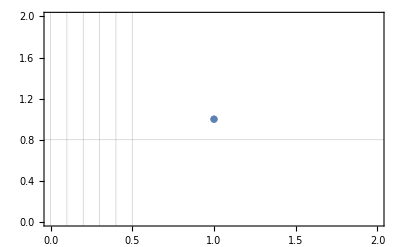

```mathematica
ParetoPrinciplePlot[{1}]
```

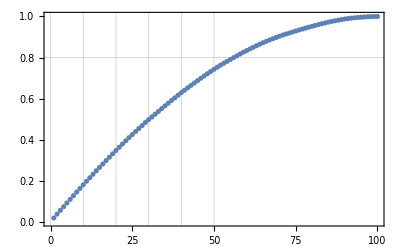

```mathematica
ParetoPrinciplePlot[RandomReal[1,100]]
```

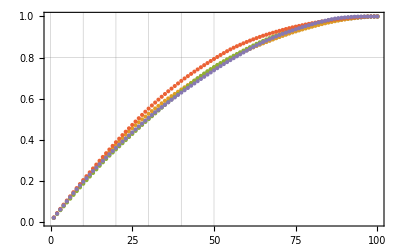

```mathematica
ParetoPrinciplePlot[Table[RandomReal[1,100],5]]
```

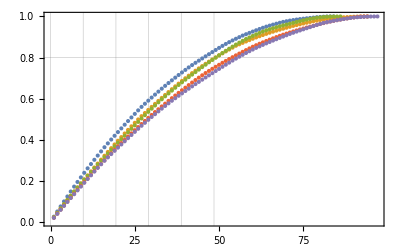

```mathematica
ParetoPrinciplePlot[Table[RandomReal[1,RandomInteger[{80,100}]],5]]
```

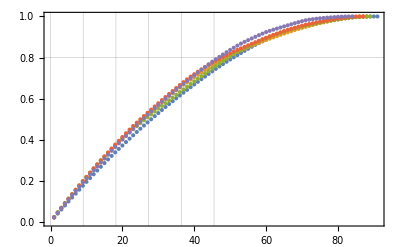

```mathematica
ParetoPrinciplePlot[Table[Tooltip[RandomReal[1,RandomInteger[{80,100}]],i],{i,1,5}]]
```

This tests that we have expected tooltips:

```mathematica
n=5;
gr=ParetoPrinciplePlot[Table[Tooltip[RandomReal[1,RandomInteger[{80,100}]],i],{i,1,n}]];
res=Cases[FullForm[gr],{Tooltip[_,_]..},∞];
Length[res]==1&&Length[res⟦1⟧]==n
```

True

#### Nested Tooltip and Callout mixed with “plain” numerical vectors

In the plot below 
1) ParetoDistribution and UniformDistribution should both tooltip and callout; 
2) PowerDistribution should have neither a tooltip nor a callout; 
3) PoissonDistribution should have a tooltip and not have a callout.

```mathematica
dists={PowerDistribution[20,0.2],ParetoDistribution[20,0.8],PoissonDistribution[12],UniformDistribution[]};
```

```mathematica
data=Map[
Switch[#,
_ParetoDistribution,
Callout[Tooltip[RandomVariate[#,RandomInteger[{800,1000}]],#],#],

_UniformDistribution,
Tooltip[Callout[RandomVariate[#,RandomInteger[{800,1000}]],#],#],

_PowerDistribution,
RandomVariate[#,RandomInteger[{800,1000}]],

_,
Tooltip[RandomVariate[#,RandomInteger[{800,1000}]],#]
]&,
dists];
```

```mathematica
ParetoPrinciplePlot[data,PlotLegends->dists,ImageSize->Large,PlotRange->All]
```

-Graphics-

#### ListPlot options

This plot of should have Pareto curves:

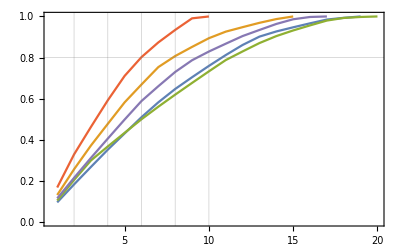

```mathematica
ParetoPrinciplePlot[Table[Tooltip[RandomReal[1,RandomInteger[{10,20}]],i],{i,1,5}],Joined->True]
```

This should be a small plot with Pareto curves and without a frames:

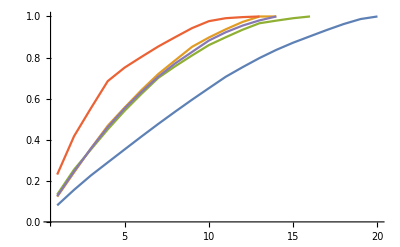

```mathematica
ParetoPrinciplePlot[Table[Tooltip[RandomReal[1,RandomInteger[{10,20}]],i],{i,1,5}],Joined->True,GridLines->None,ImageSize->Tiny,Frame->None]
```

#### "ParetoGridLines"

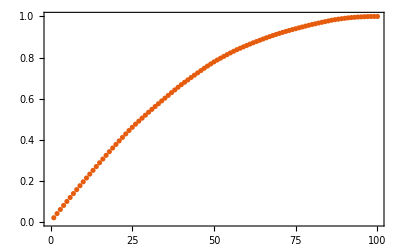

```mathematica
ParetoPrinciplePlot[RandomReal[1,100],PlotTheme->"Scientific","ParetoGridLines"->{Range[0,1,0.05],Range[0,1,0.05]}]
```

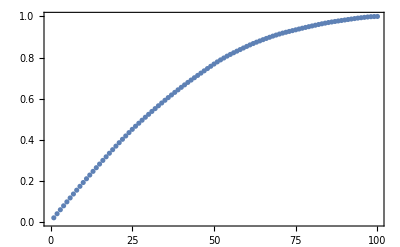

```mathematica
ParetoPrinciplePlot[RandomReal[1,100],"ParetoGridLines"->{None,None}]
```

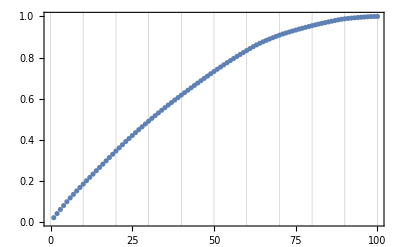

```mathematica
ParetoPrinciplePlot[RandomReal[1,100],"ParetoGridLines"->{Automatic,None}]
```

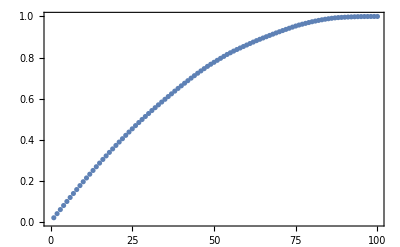

```mathematica
ParetoPrinciplePlot[RandomReal[1,100],"ParetoGridLines"->None]
```

#### These are expected to fail

```mathematica
ParetoPrinciplePlot[BlahBlah]
```

ParetoPrinciplePlot::args: The first argument is expected to be a numerical vector or a list of numerical vectors.

$Failed

```mathematica
ParetoPrinciplePlot[RandomWord[23]]
```

ParetoPrinciplePlot::args: The first argument is expected to be a numerical vector or a list of numerical vectors.

$Failed

#### These produce messages but do not fail

Power::infy: Infinite expression 1/0 encountered.

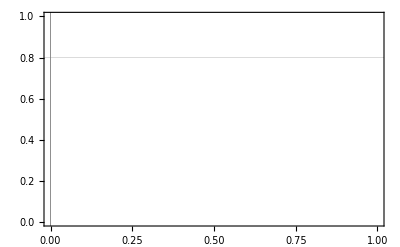

```mathematica
ParetoPrinciplePlot[{}]
```

ParetoPrinciplePlot::pgl: The value of the option "ParetoGridLines" is expected to be Automatic or a list of two numerical vectors, each with numbers between 0 and 1.

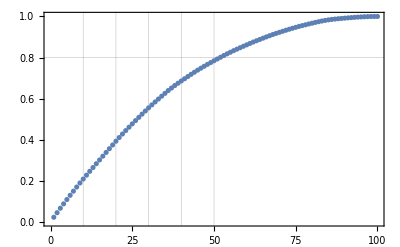

```mathematica
ParetoPrinciplePlot[RandomReal[1,100],"ParetoGridLines"->{Range[0,109],RandomWord[23]}]
```

ParetoPrinciplePlot::pgl: The value of the option "ParetoGridLines" is expected to be Automatic or a list of two numerical vectors, each with numbers between 0 and 1.

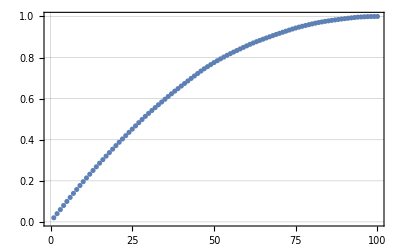

```mathematica
ParetoPrinciplePlot[RandomReal[1,100],"ParetoGridLines"->{Range[0,0.7],Range[0,2,0.2]}]
```

ParetoPrinciplePlot::pgl: The value of the option "ParetoGridLines" is expected to be Automatic or a list of two numerical vectors, each with numbers between 0 and 1.

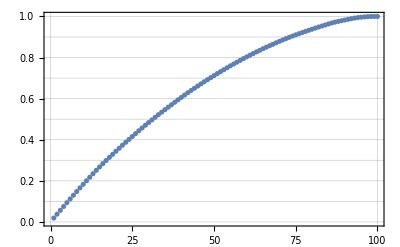

```mathematica
ParetoPrinciplePlot[RandomReal[1,100],"ParetoGridLines"->{Range[0,7],Automatic}]
```

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.